```mathematica
dat=ReadList["V0=0.3.dat"];
datSolitons=Import["BS.txt","Table"];
zeroMode=Import["zero-mode-V0=0.3.dat","Table"];
extremalHBH = ReadList["extremal-V0=0.3.dat"];
```

```mathematica
V=0.3;
```

```mathematica
lenZM=Length[zeroMode];
rhZM=zeroMode[[All,-3]];
aZM=zeroMode[[All,-2]];
wZM=aZM/(aZM*aZM+rhZM*rhZM);
QeZM=V*(aZM*aZM+rhZM*rhZM)/rhZM;
MZM=(aZM*aZM+rhZM*rhZM+QeZM*QeZM)/(2*rhZM);
JZM=aZM*MZM;
```

```mathematica
extremalKN[x_]:=Sqrt[((1.0-4.0*V*V+Sqrt[(1.0+8.0*V*V)])/x)]/(2.0*Sqrt[(2.0*x)])
```

```mathematica
lenExtremal=Length[extremalHBH];
extremalw=extremalHBH[[All,1]];
extremalMass=extremalHBH[[All,3]];
extremalMH=extremalHBH[[All,4]];
extremalJ=extremalHBH[[All,5]];
extremalJH=extremalHBH[[All,6]];
extremalg=extremalHBH[[All,14]];
extremalQeINF=extremalHBH[[All,11]];
```

```mathematica
w=dat[[All,1]];
V0=dat[[All,2]];
Mass=dat[[All,3]];
MH=dat[[All,4]];
J=dat[[All,5]];
JH=dat[[All,6]];
Mint=-dat[[All,7]];
MintM=dat[[All,8]];
Mints=dat[[All,9]];
Jint=dat[[All,10]];
JintM=dat[[All,11]];
Jints=dat[[All,12]];
TH=dat[[All,13]];
AH=dat[[All,14]];
QeINF=dat[[All,15]];
muINF=dat[[All,16]];
rh=dat[[All,17]];
g=dat[[All,18]];
```

```mathematica
wSolitons = datSolitons[[All,1]];
MSolitons = datSolitons[[All,2]];
JSolitons = datSolitons[[All,3]];
```

```mathematica
len=Length[dat];
lenSolitons=Length[datSolitons];
```

```mathematica
solitonwM=ListPlot[Table[{wSolitons[[i]],MSolitons[[i]]},{i,1,lenSolitons}],PlotStyle->  Red,Joined->True];
zeroModePlot = ListPlot[Table[{wZM[[i]],MZM[[i]]},{i,1,lenZM}],PlotStyle->{Blue,Dashed},Joined->True];
extremalKNPlot = Plot[extremalKN[x],{x,0,1},PlotStyle->Black];
extremalHBHplot = ListPlot[Table[{extremalw[[i]],extremalMass[[i]]},{i,1,lenExtremal}],PlotStyle->Green,Joined->True];
```

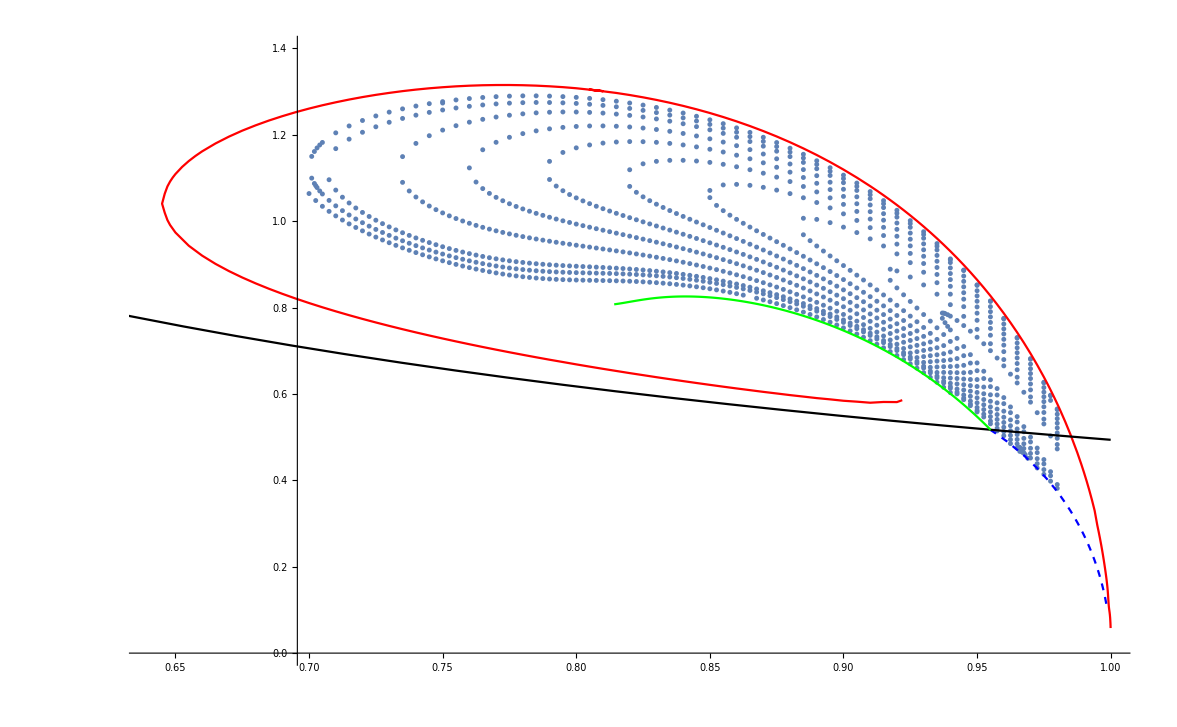

```mathematica
m=ListPlot[Table[{w[[i]],Mass[[i]]},{i,1,len}],PlotStyle->PointSize[0.003]];
Show[m,solitonwM,zeroModePlot,extremalKNPlot,extremalHBHplot,PlotRange->{{0.64,1},{0.,1.4}}]
```

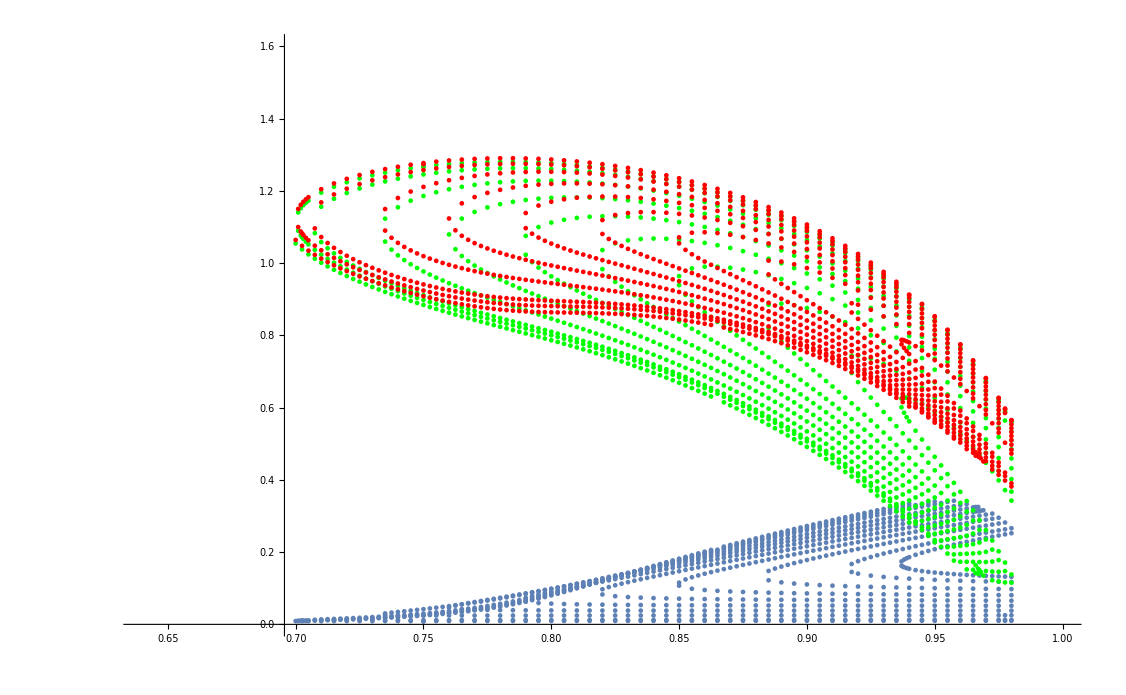

```mathematica
p1=ListPlot[Table[{w[[i]],MH[[i]]},{i,1,len}],PlotStyle->PointSize[0.003]];
p2=ListPlot[Table[{w[[i]],Mint[[i]]},{i,1,len}],PlotStyle->{Green,PointSize[0.003]}];
p3=ListPlot[Table[{w[[i]],Mass[[i]]},{i,1,len}],PlotStyle->{Red,PointSize[0.003]}];
Show[p1,p2,p3,PlotRange->{{0.64,1},{0,1.6}}]
```

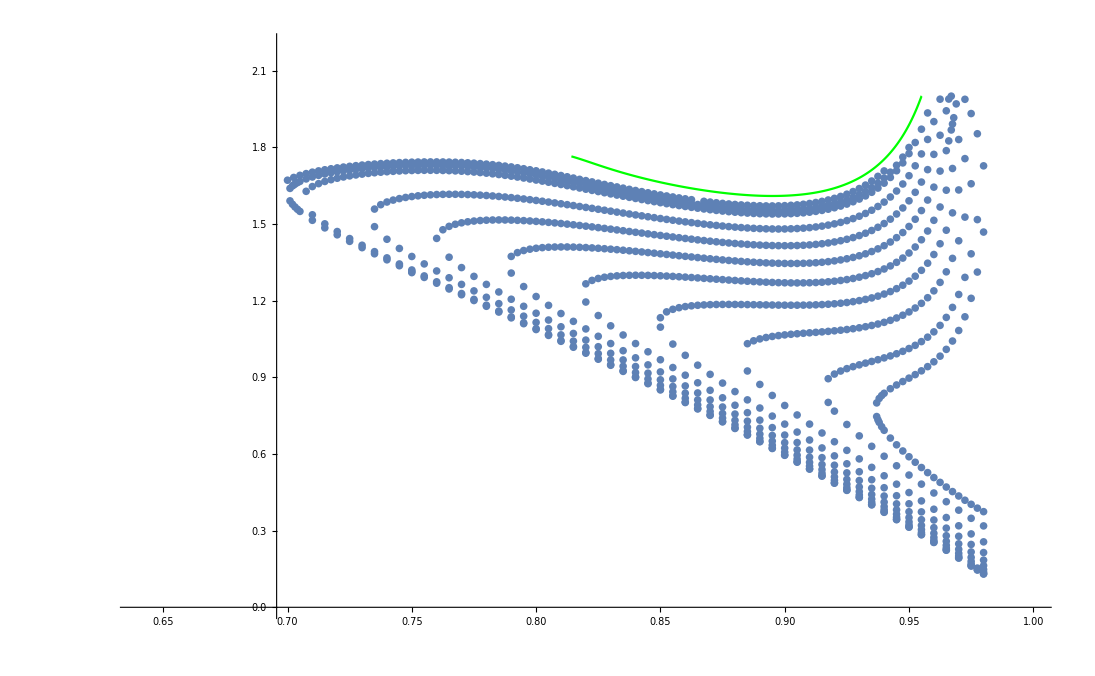

```mathematica
gPlot=ListPlot[Table[{w[[i]],g[[i]]},{i,1,len}],PlotStyle->PointSize[0.005]];
extremalgPlot=ListPlot[Table[{extremalw[[i]],extremalg[[i]]},{i,1,lenExtremal}],PlotStyle->Green,Joined->True];
Show[gPlot,extremalgPlot,PlotRange->{{0.64,1},{0.,2.2}}]
```

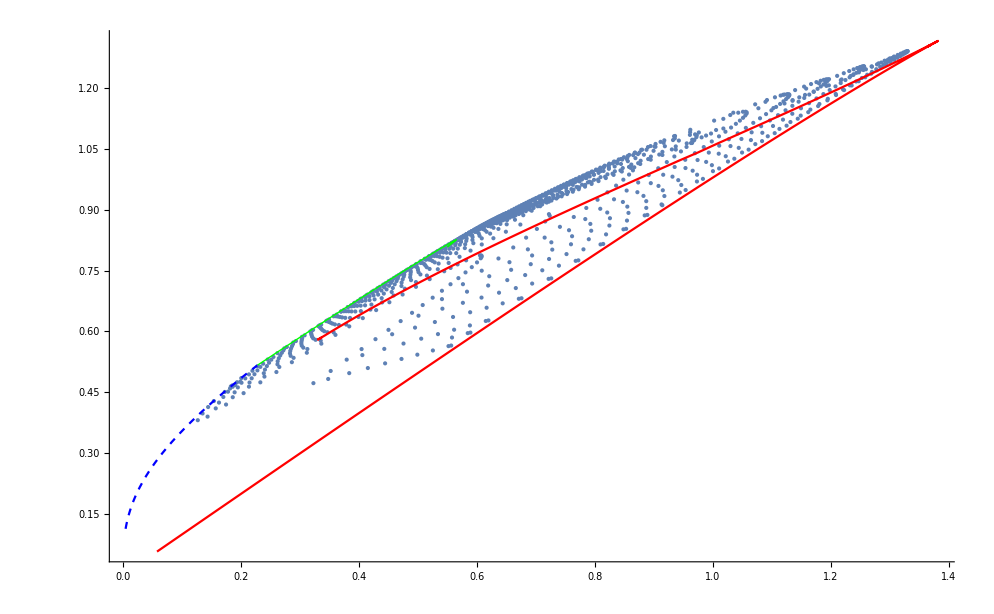

```mathematica
p1 = ListPlot[Table[{extremalJ[[i]],extremalMass[[i]]},{i,1,lenExtremal}],PlotStyle->{Green,Thick},Joined->True];
p2 =ListPlot[Table[{J[[i]],Mass[[i]]},{i,1,len}],PlotStyle->PointSize[0.003]];
p3 = ListPlot[Table[{JZM[[i]],MZM[[i]]},{i,1,lenZM}],PlotStyle->{Blue,Dashed},Joined->True];
p4 = ListPlot[Table[{JSolitons[[i]],MSolitons[[i]]},{i,1,lenSolitons}],PlotStyle->{Red},Joined->True];
Show[p2,p1,p3,p4,PlotRange->Automatic,AxesOrigin-> {0,0}]
```

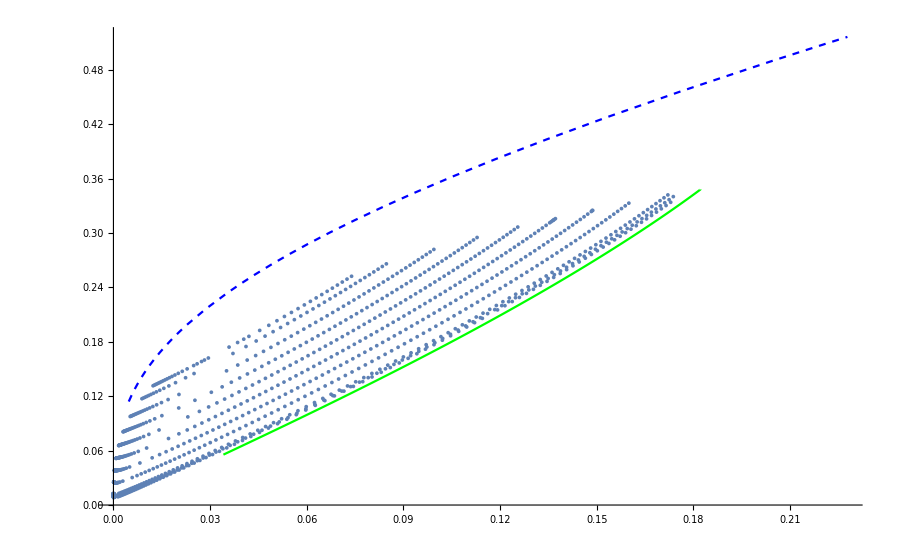

```mathematica
p1 = ListPlot[Table[{extremalJH[[i]],extremalMH[[i]]},{i,1,lenExtremal}],PlotStyle->Green,Joined->True];
p2 =ListPlot[Table[{JH[[i]],MH[[i]]},{i,1,len}],PlotStyle->PointSize[0.003]];
p3 = ListPlot[Table[{JZM[[i]],MZM[[i]]},{i,1,lenZM}],PlotStyle->{Blue,Dashed},Joined->True];
Show[p1,p2,p3,PlotRange->Automatic,AxesOrigin-> {0,0}]
```

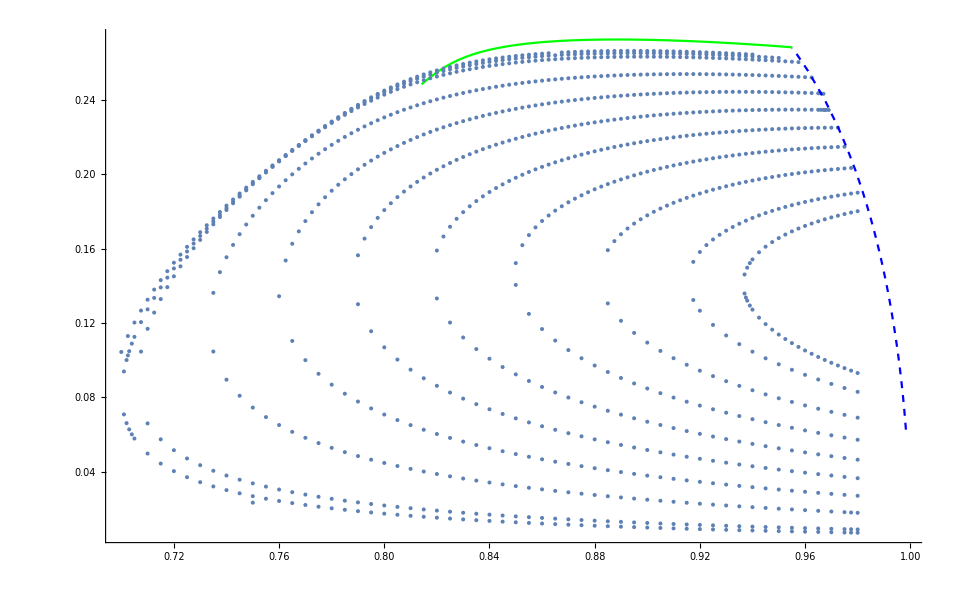

```mathematica
p1 = ListPlot[Table[{extremalw[[i]],-extremalQeINF[[i]]},{i,1,lenExtremal}],PlotStyle->Green,Joined->True];
p2 =ListPlot[Table[{w[[i]],-QeINF[[i]]},{i,1,len}],PlotStyle->PointSize[0.003]];
p3 = ListPlot[Table[{wZM[[i]],QeZM[[i]]},{i,1,lenZM}],PlotStyle->{Blue,Dashed},Joined->True];
Show[p1,p2,p3,PlotRange->Automatic,AxesOrigin-> {0.69,0}]
```

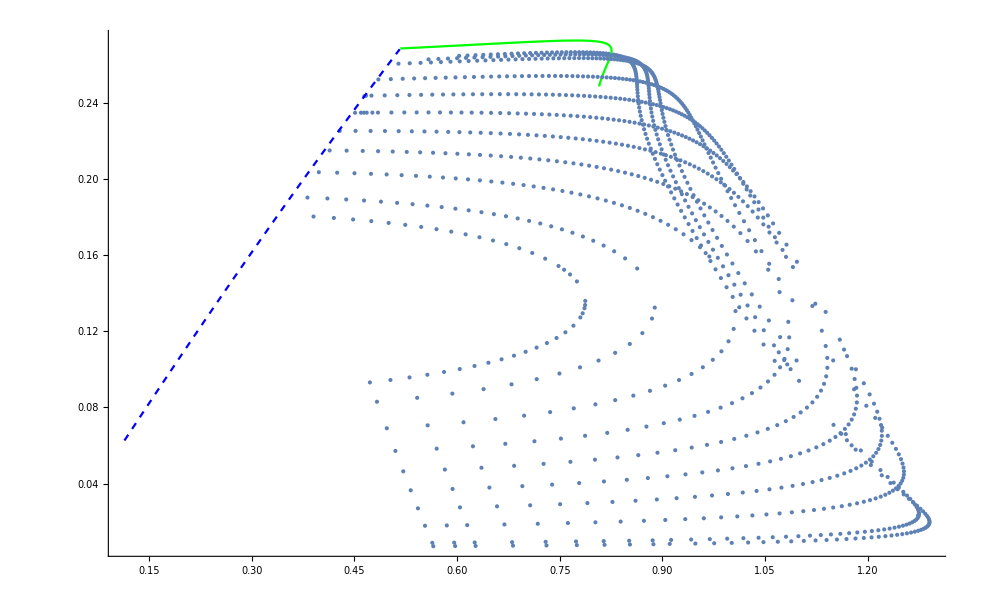

```mathematica
p1 = ListPlot[Table[{extremalMass[[i]],-extremalQeINF[[i]]},{i,1,lenExtremal}],PlotStyle->Green,Joined->True];
p2 =ListPlot[Table[{Mass[[i]],-QeINF[[i]]},{i,1,len}],PlotStyle->PointSize[0.003]];
p3 = ListPlot[Table[{MZM[[i]],QeZM[[i]]},{i,1,lenZM}],PlotStyle->{Blue,Dashed},Joined->True];
Show[p1,p2,p3,PlotRange->Automatic,AxesOrigin-> {0,0}]
```

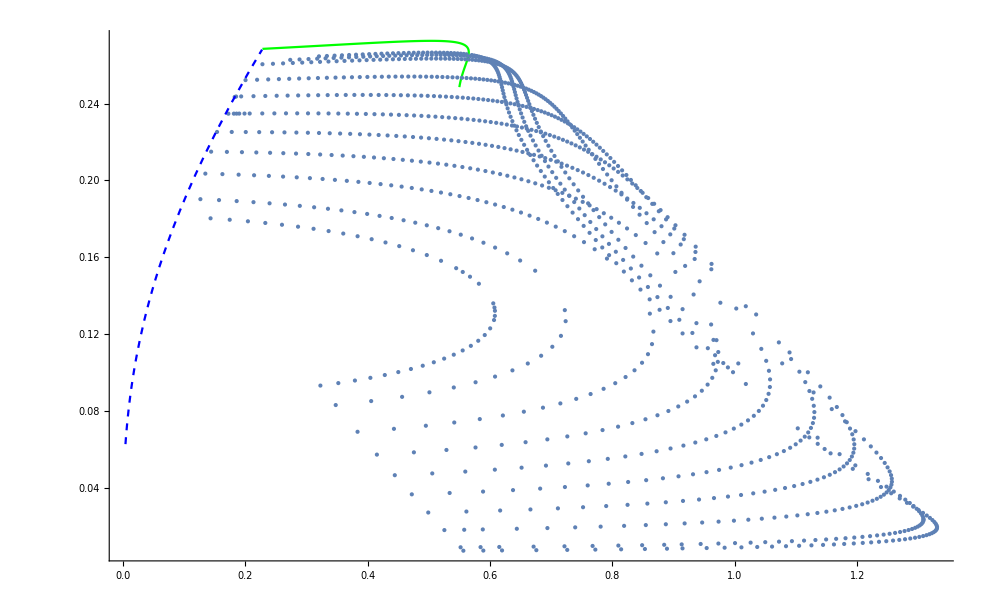

```mathematica
p1 = ListPlot[Table[{extremalJ[[i]],-extremalQeINF[[i]]},{i,1,lenExtremal}],PlotStyle->Green,Joined->True];
p2 =ListPlot[Table[{J[[i]],-QeINF[[i]]},{i,1,len}],PlotStyle->PointSize[0.003]];
p3 = ListPlot[Table[{JZM[[i]],QeZM[[i]]},{i,1,lenZM}],PlotStyle->{Blue,Dashed},Joined->True];
Show[p1,p2,p3,PlotRange->Automatic,AxesOrigin-> {0,0}]
```